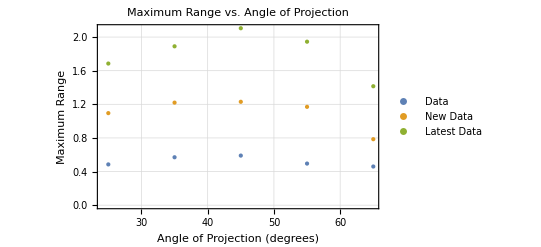

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

angles=data[[All,1]];  (*Assuming the first element of each sublist is the angle in degrees*)
ranges1=data[[All,2]];
ranges2=newData[[All,2]];
ranges3=latestData[[All,2]];

ListPlot[{Transpose[{angles,ranges1}],Transpose[{angles,ranges2}],Transpose[{angles,ranges3}]},PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium]},PlotLegends->{"Data","New Data","Latest Data"},Frame->True,GridLines->Automatic,FrameLabel->{"Angle of Projection (degrees)","Maximum Range"},PlotLabel->"Maximum Range vs. Angle of Projection"]
```

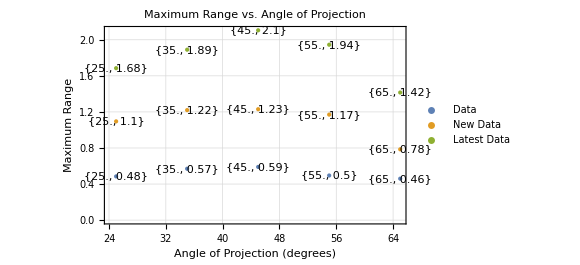

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

angles=data[[All,1]];  (*Assuming the first element of each sublist is the angle in degrees*)
ranges1=data[[All,2]];
ranges2=newData[[All,2]];
ranges3=latestData[[All,2]];

ListPlot[{Transpose[{angles,ranges1}],Transpose[{angles,ranges2}],Transpose[{angles,ranges3}]},PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium]},PlotLegends->{"Data","New Data","Latest Data"},Frame->True,GridLines->Automatic,FrameLabel->{"Angle of Projection (degrees)","Maximum Range"},PlotLabel->"Maximum Range vs. Angle of Projection",Epilog->{Text[ToString[Round[{#,#2},0.01]],{#,#2},{-1,0}]&@@@Transpose[{angles,ranges1}],Text[ToString[Round[{#,#2},0.01]],{#,#2},{-1,0}]&@@@Transpose[{angles,ranges2}],Text[ToString[Round[{#,#2},0.01]],{#,#2},{-1,0}]&@@@Transpose[{angles,ranges3}]}]
```

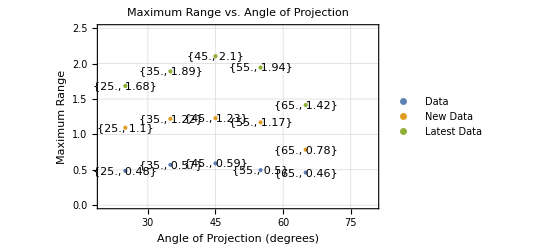

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

angles=data[[All,1]];  (*Assuming the first element of each sublist is the angle in degrees*)
ranges1=data[[All,2]];
ranges2=newData[[All,2]];
ranges3=latestData[[All,2]];

ListPlot[{Transpose[{angles,ranges1}],Transpose[{angles,ranges2}],Transpose[{angles,ranges3}]},PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium]},PlotLegends->{"Data","New Data","Latest Data"},Frame->True,GridLines->Automatic,FrameLabel->{"Angle of Projection (degrees)","Maximum Range"},PlotLabel->"Maximum Range vs. Angle of Projection",Epilog->{Text[ToString[Round[{#,#2},0.01]],{#,#2},{-1,0}]&@@@Transpose[{angles,ranges1}],Text[ToString[Round[{#,#2},0.01]],{#,#2},{-1,0}]&@@@Transpose[{angles,ranges2}],Text[ToString[Round[{#,#2},0.01]],{#,#2},{-1,0}]&@@@Transpose[{angles,ranges3}]},PlotRange->{{20,80},{0,2.5}}  (*Adjust the axis ranges as needed*)]
```